```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
a={{Subscript[X, 1,7](*+Subscript[X, 7,7]*),Subscript[X, 2,1](*+Subscript[X, 2,100]*),Subscript[X, 3,2](*+Subscript[X, 2,1]*)(*+Subscript[Z, 30]*),Subscript[X, 8,3](*+Subscript[X, 8,3]*),0,0,0},{Subscript[X, 13,1],Subscript[X, 1,4],0,0,Subscript[X, 4,13],0,0},{0,Subscript[X, 4,2],Subscript[X, 2,5],0,0,Subscript[X, 5,4],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,6],0,0,Subscript[X, 6,5]},{0,0,0,0,Subscript[X, 12,4],Subscript[X, 4,11],0},{0,0,0,0,0,Subscript[X, 11,5],Subscript[X, 5,10]},{0,0,0,Subscript[X, 6,9],0,0,Subscript[X, 10,6]}}/.formatrule;
b={{0,0,0,Subscript[X, 7,8]},{0,0,0,0},{0,0,0,0},{0,0,0,0},{Subscript[X, 11,12],0,0,0},{0,Subscript[X, 10,11],0,0},{0,0,Subscript[X, 9,10],0}}/.formatrule;
c={{Subscript[X, 7,13],0,0,0,0,0,0},{0,0,0,Subscript[X, 9,8],0,0,0},{0,0,0,0,Subscript[X, 13,12],0,0}}/.formatrule;
d={{0,0,0,0},{0,0,0,0},{0,0,0,0}}/.formatrule;
```

```mathematica
moduliGauging2[a,b,c,d]
```

K_0 = (X[1,7] | X[2,1] | X[3,2] | X[8,3] | 0 | 0 | 0 | 0 | 0 | 0 | X[7,8]
X[13,1] | X[1,4] | 0 | 0 | X[4,13] | 0 | 0 | 0 | 0 | 0 | 0
0 | X[4,2] | X[2,5] | 0 | 0 | X[5,4] | 0 | 0 | 0 | 0 | 0
0 | 0 | X[5,3] | X[3,6] | 0 | 0 | X[6,5] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | X[12,4] | X[4,11] | 0 | X[11,12] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | X[11,5] | X[5,10] | 0 | X[10,11] | 0 | 0
0 | 0 | 0 | X[6,9] | 0 | 0 | X[10,6] | 0 | 0 | X[9,10] | 0
X[7,13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | X[9,8] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | X[13,12] | 0 | 0 | 0 | 0 | 0 | 0)

Matrix is OK, there are no doubles.

Part::partw: Part 3 of X[1, 7] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Mistake in row 1 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 2 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 3 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 4 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 5 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 6 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 7 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 1 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 2 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 3 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 4 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 5 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 6 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 7 of Kasteleyn! Someone has a wrong name, or there's an extra field.

There are 110 perfect matchings.

-------------------------------------

Variables are 'perf'=determinant of Kasteleyn matrix; 'plist'=list of perfect matchings; 'P'=perfect matching matrix; 'Xlist'=fields corresponding to the rows of P; 'moduliP'=P but only with rows corresponding to external X_(i, j)'s; 'remainingP'=P but only with rows corresponding to internal X_(i, j)'s; similarly for Xremain and Xmoduli; 'xb'=list of external fields;

-------------------------------------

The Master space is 12-dimensional. (NB This is the dimension of its toric diagram!).

G = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

The moduli space is 6-dimensional. (NB This is the dimension of its toric diagram!).

-------------------------------------

Variables are 'Gmaster'=master space; 'Gmoduli'=moduli space; 'Gshort'=moduli space where doubles have been removed; 'Multmatrix'=moultiplicity of each point in Gshort;

-------------------------------------

```mathematica
Position[plist,X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] X[9,8] X[9,10]]
```

{{22}}

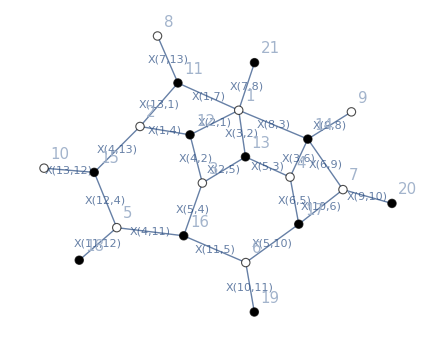

```mathematica
drawBFT[a,b,c,d]
```

```mathematica
pmref=plist[[22]]
order={8,10,18,19,20,9,21};
boundaries={order};
boundarycuts={};
```

X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] X[9,8] X[9,10]

```mathematica
pathmatrix[a,b,c,d,pmref,order]
Print["This is the path matrix 'pathmat':"];
Print[pathmat//MatrixForm];
sources=findSources[a,b,c,d,order,pmref];
sinks=findSinks[a,b,c,d,order,pmref];

(*Now make it nicer and plug in Postnikov's signs*)
(*First make the replacement lists.*)
therule=MapThread[Rule,{plist,Table[Subscript[pp, i],{i,Length[plist]}]}];(*To recognize stuff as perfect matchings*)
inverserule=MapThread[Rule,{Table[Subscript[pp, i],{i,Length[plist]}],plist/pmref}];
repl=MapThread[Rule,{Xlist,ConstantArray[1,Length[Xlist]]}];(*This is needed to get the signs right*)
(*This is for Postnikov's signs*)
newnumberrule=MapThread[Rule,{order,Range[Length[order]]}];
newsource=sources/.newnumberrule;
(*Make the rule for the replacement of loops with variables Subscript[loop, i]*)
looprep={};
invlooprep={};
loopflip={};
looplist=MapThread[Times,{(MonomialList[Expand[loops pmref]]/pmref)/.repl,MonomialList[Expand[loops pmref]]/pmref}];
dummy=1;
For[i=1,i<Length[looplist]+1,i++,
If[looplist[[i]]==1,True,True,
Subscript[l, dummy]=looplist[[i]];
looprep=Join[looprep,{Subscript[l, dummy]->Subscript[loop, dummy]}];
invlooprep=Join[invlooprep,{Subscript[loop, dummy]->Subscript[l, dummy]}];
loopflip=Join[loopflip,{Subscript[loop, dummy]->-Subscript[loop, dummy]}];
dummy=dummy+1;
];
];

postnikovpath=pathmat;(*this will be the path matrix with postnikov's signs incorporated*)
For[i=1,i<Length[sources]+1,i++,(*Rows of the sign matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the sign matrix*)
(*This is to get Postnikov's signs*)
count=0;
For[k=1,k<Length[sources]+1,k++,
If[Min[newsource[[i]],j]<newsource[[k]]&&newsource[[k]]<Max[newsource[[i]],j],count=count+1;];
];
(*This is to make it look nice, and plug in the overall signs.*)
If[pathmat[[i,j]]==1||pathmat[[i,j]]==0,True,True,
If[Denominator[pathmat[[i,j]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[pathmat[[i,j]]]+1,k++,
If[Length[MonomialList[Denominator[pathmat[[i,j]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{Expand[Simplify[pathmat[[i,j]][[k]]loops]]/loops}];
,terms=Join[terms,{pathmat[[i,j]][[k]]}];(*If we don't have loops*)
];
];
postnikovpath[[i,j]]=Total[terms](-1)^count;
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[pathmat[[i,j]]]]]>1,
(*If the term has loops*)
postnikovpath[[i,j]]=(-1)^count Expand[Simplify[pathmat[[i,j]]loops]]/loops;
,postnikovpath[[i,j]]=(-1)^count pathmat[[i,j]];
];
];
];
(*Done looking nice, and overall signs!*)
];
];
postnikovpathloop=postnikovpath;
(*Now replace loops in postnikovpathloop with Subscript[loop, i] variables*)
change=1;(*Keeps track of whether postnikovpathloop changed when we gave it loopreplacements*)
compa=postnikovpathloop;(*This is what we compare with*)
While[change==1,
postnikovpathloop=postnikovpathloop/.looprep;
If[compa==postnikovpathloop,(*if putting in loop replacement changed nothing, we've replaced all the loops that can be replaced*)
change=0;
];
compa=postnikovpathloop;
];
postnikovpathloop=postnikovpathloop/.loopflip;
postnikovpath=postnikovpathloop/.invlooprep;
Print["Path matrix with Postnikov's overall signs, and signs for loops 'postnikovpath':"];
Print[postnikovpath//MatrixForm];
(*Print[postnikovpathloop//MatrixForm];*)

(*Now plug  in Gekhtman's signs*)
numtoorder=MapThread[Rule,{order,Range[Length[order]]}];
postgekhtmatrixloop=postnikovpathloop;
For[i=1,i<Length[sources]+1,i++,(*Rows of the matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the matrix*)
If[postnikovpathloop[[i,j]]==1||postnikovpathloop[[i,j]]==0,True,True,
bguys={};
(*Now find out which boundaries this entries goes between.*)
For[k=1,k<Length[boundaries]+1,k++,
If[MemberQ[boundaries[[k]],sources[[i]]]||MemberQ[boundaries[[k]],order[[j]]],
bguys=Join[bguys,{k}];
];
];
bguys=Sort[bguys];
(*If[i==1&&(j==5||j==4),Print["bguys=",bguys];];*)
If[Length[bguys]==2,(*Only do it if we re going between different boundaries*)
postgekhtmatrixloop[[i,j]]=postnikovpathloop[[i,j]]/.(bguys/.boundarycuts);
];
];
];
];
postgekhtmatrix=postgekhtmatrixloop/.invlooprep;
Print["This is the matrix with also include Gekhtmans's signs 'postgekhtmatrix':"];
Print[postgekhtmatrix//MatrixForm];

(*Now write it up nicely in terms of pms.*)
tempmat=Expand[Simplify[postgekhtmatrix]];
pmpostgekhtmatrix=postgekhtmatrix;
pmloops=((Total[looplist pmref]/.therule)/.{Subscript[pp, Position[plist,pmref][[1,1]]]->1});
For[i=1,i<Length[sources]+1,i++,(*Rows of the sign matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the sign matrix*)
If[tempmat[[i,j]]==1||tempmat[[i,j]]==0,True,True,
If[Denominator[tempmat[[i,j]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[tempmat[[i,j]]]+1,k++,
If[Length[MonomialList[Denominator[tempmat[[i,j]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{((Expand[Simplify[tempmat[[i,j]][[k]]Total[looplist]]]pmref)/.therule)/pmloops}];
,terms=Join[terms,{((tempmat[[i,j]][[k]]pmref)/.therule)}];(*If we don't have loops*)
];
];
pmpostgekhtmatrix[[i,j]]=Total[terms];
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[tempmat[[i,j]]]]]>1,
(*If the term has loops*)
pmpostgekhtmatrix[[i,j]]=((Expand[Simplify[tempmat[[i,j]]Total[looplist]]] pmref)/.therule)/pmloops;
,pmpostgekhtmatrix[[i,j]]=((tempmat[[i,j]] pmref)/.therule);
];
];
];
(*Done looking nice, and overall signs!*)
];
];
Print["The Grassmannian matrix in terms of perfect matchings is 'pmpostgekhtmatrix':"];
Print[pmpostgekhtmatrix//MatrixForm];

(*Now calculate the Pluckers!*)
plucker=Expand[Simplify[Minors[postgekhtmatrix,Length[sources]][[1]]]];
Print["These are the Pluckers 'plucker':"];
Print[plucker//MatrixForm];

(*Now make the Pluckers look nice*)
niceplucker=plucker;
For[i=1,i<Length[plucker]+1,i++,(*Rows of the sign matrix*)
If[plucker[[i]]==1,True,True,
If[Denominator[plucker[[i]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[plucker[[i]]]+1,k++,
If[Length[MonomialList[Denominator[plucker[[i]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{((Expand[Simplify[plucker[[i]][[k]]Total[looplist]]]pmref)/.therule)/pmloops}];
,terms=Join[terms,{((plucker[[i]][[k]]pmref)/.therule)}];(*If we don't have loops*)
];
];
niceplucker[[i]]=Total[terms];
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[plucker[[i]]]]]>1,
(*If the term has loops*)
niceplucker[[i]]=((Expand[Simplify[plucker[[i]]Total[looplist]]] pmref)/.therule)/pmloops;
,niceplucker[[i]]=((plucker[[i]] pmref)/.therule);
];
];
];
(*Done looking nice, and overall signs!*)
];
Print["Pluckers written in terms of perfect matchings 'niceplucker':"];
Print[niceplucker//MatrixForm];
realplucker=Expand[Simplify[plucker Total[looplist]pmref]]/.therule;
Print["Real map between Pluckers and perfect matchings 'realplucker':"];
Print[realplucker//MatrixForm];

(*Now check that the Pluckers are correct, i.e. that they all have the correct source set.*)
kmat=Join[Join[a,c],Join[b,d],2];
btra=Transpose[b];
xtonum={};
For[i=1,i<Length[c]+1,i++,
xtonum=Join[xtonum,{(i+Length[a])->DeleteCases[c[[i]],0][[1]]}];
];
For[j=1,j<Length[btra]+1,j++,
xtonum=Join[xtonum,{(j+Length[a]+Length[c]+Dimensions[a][[2]])->DeleteCases[btra[[j]],0][[1]]}];
];
xorder=order/.xtonum;
ordering=MapThread[Rule,{xorder,Range[Length[order]]}];
(*Done with the first part! Now check source sets...*)
subs=Subsets[Range[Length[order]],{Length[sources]}];
compare={};
For[i=1,i<Length[realplucker]+1,i++,
guys=MapThread[Times,{MonomialList[realplucker[[i]]]/.Table[Subscript[pp, x]->1,{x,Length[plist]}],MonomialList[realplucker[[i]]]}];
For[j=1,j<Length[guys]+1,j++,
compare=Join[compare,{guys[[j]][[2]]->subs[[i]]}];
];
];
compare=Sort[compare];
If[compare==pmsourcesOrderingByHand[a,b,c,d,ordering],
Print["Checked that the source set for these perfect matchings is indeed the Plucker coordiate in question, OK!"];
,Print["It seems like the source set of some of these perfect matchings is NOT the correct Plucker coordinate...CHECK IT!"];
];
```

The full path matrix is 'fullmatrix', the part that goes from sources to sinks is 'pathmat', the loop denominator is 'loops'.

This is the path matrix 'pathmat':

((X[4,2] X[4,11] X[5,3] X[5,10] X[13,1] X[13,12])/(X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 1 | -(X[1,4] X[5,3] X[5,4] X[5,10] X[11,12] X[13,12])/(-X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])-(X[1,4] X[2,5] X[6,5] X[11,5] X[11,12] X[13,12])/(-X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]) | -(X[1,4] X[2,5] X[4,11] X[6,5] X[10,11] X[13,12])/(-X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]) | 0 | (X[1,4] X[2,5] X[3,6] X[4,11] X[5,10] X[13,12])/(X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 0
(X[4,2] X[5,3] X[10,6] X[11,5] X[12,4] X[13,1])/(X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 0 | (X[4,2] X[4,13] X[5,3] X[10,6] X[11,5] X[11,12])/(X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | (X[4,2] X[4,11] X[4,13] X[5,3] X[10,6] X[10,11])/(X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[5,3] X[5,4] X[10,6] X[10,11] X[12,4])/(X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 1 | (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[6,9])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[5,3] X[5,4] X[5,10] X[6,9] X[12,4])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[2,5] X[6,5] X[6,9] X[11,5] X[12,4])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[3,6] X[10,6] X[11,5] X[12,4])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 0
(X[1,7] X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[1,7] X[5,3] X[5,4] X[5,10] X[12,4])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[1,7] X[2,5] X[6,5] X[11,5] X[12,4])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[5,3] X[5,4] X[5,10] X[12,4] X[13,1])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[6,5] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[6,5] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 0 | (X[2,1] X[4,13] X[5,3] X[5,4] X[5,10] X[11,12])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[4,13] X[6,5] X[11,5] X[11,12])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,13] X[6,5] X[11,5] X[11,12])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | (X[2,1] X[2,5] X[4,11] X[4,13] X[6,5] X[10,11])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,11] X[4,13] X[6,5] X[10,11])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[3,2] X[5,4] X[6,5] X[10,11] X[12,4])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 0 | (X[2,1] X[2,5] X[3,6] X[4,11] X[4,13] X[5,10])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[4,11] X[4,13] X[5,10])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[8,3])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[3,2] X[3,6] X[5,4] X[5,10] X[12,4])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[5,3] X[5,4] X[5,10] X[8,3] X[12,4])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))-(X[1,4] X[2,5] X[6,5] X[8,3] X[11,5] X[12,4])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]-X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])) | 1)

Path matrix with Postnikov's overall signs, and signs for loops 'postnikovpath':

((X[13,1] X[13,12])/(X[4,13] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 1 | (X[1,4] X[5,4] X[11,12] X[13,12])/(X[4,2] X[4,11] X[4,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[6,5] X[11,5] X[11,12] X[13,12])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | (X[1,4] X[2,5] X[6,5] X[10,11] X[13,12])/(X[4,2] X[4,13] X[5,3] X[5,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | -(X[1,4] X[2,5] X[3,6] X[13,12])/(X[4,2] X[4,13] X[5,3] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0
-(X[10,6] X[11,5] X[12,4] X[13,1])/(X[4,11] X[4,13] X[5,10] X[7,13] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | (X[10,6] X[11,5] X[11,12])/(X[4,11] X[5,10] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | (X[10,6] X[10,11])/(X[5,10] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[5,4] X[10,6] X[10,11] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,10] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 1 | X[6,9]/(X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[5,4] X[6,9] X[12,4])/(X[4,2] X[4,11] X[4,13] X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[6,5] X[6,9] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[3,6] X[10,6] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0
X[1,7]/(X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[1,7] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[1,7] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[2,1] X[5,4] X[12,4] X[13,1])/(X[4,2] X[4,11] X[4,13] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[3,2] X[6,5] X[11,5] X[12,4] X[13,1])/(X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[2,1] X[2,5] X[6,5] X[11,5] X[12,4] X[13,1])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | -(X[2,1] X[5,4] X[11,12])/(X[4,2] X[4,11] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[3,2] X[6,5] X[11,5] X[11,12])/(X[4,11] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[2,1] X[2,5] X[6,5] X[11,5] X[11,12])/(X[4,2] X[4,11] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | -(X[3,2] X[6,5] X[10,11])/(X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[2,1] X[2,5] X[6,5] X[10,11])/(X[4,2] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[1,4] X[3,2] X[5,4] X[6,5] X[10,11] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | (X[3,2] X[3,6])/(X[5,3] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[2,1] X[2,5] X[3,6])/(X[4,2] X[5,3] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+X[8,3]/(X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[3,2] X[3,6] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[5,4] X[8,3] X[12,4])/(X[4,2] X[4,11] X[4,13] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[6,5] X[8,3] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 1)

This is the matrix with also include Gekhtmans's signs 'postgekhtmatrix':

((X[13,1] X[13,12])/(X[4,13] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 1 | (X[1,4] X[5,4] X[11,12] X[13,12])/(X[4,2] X[4,11] X[4,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[6,5] X[11,5] X[11,12] X[13,12])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | (X[1,4] X[2,5] X[6,5] X[10,11] X[13,12])/(X[4,2] X[4,13] X[5,3] X[5,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | -(X[1,4] X[2,5] X[3,6] X[13,12])/(X[4,2] X[4,13] X[5,3] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0
-(X[10,6] X[11,5] X[12,4] X[13,1])/(X[4,11] X[4,13] X[5,10] X[7,13] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | (X[10,6] X[11,5] X[11,12])/(X[4,11] X[5,10] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | (X[10,6] X[10,11])/(X[5,10] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[5,4] X[10,6] X[10,11] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,10] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 1 | X[6,9]/(X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[5,4] X[6,9] X[12,4])/(X[4,2] X[4,11] X[4,13] X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[6,5] X[6,9] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[3,6] X[10,6] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[9,8] X[9,10] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0
X[1,7]/(X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[1,7] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[1,7] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[2,1] X[5,4] X[12,4] X[13,1])/(X[4,2] X[4,11] X[4,13] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[3,2] X[6,5] X[11,5] X[12,4] X[13,1])/(X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[2,1] X[2,5] X[6,5] X[11,5] X[12,4] X[13,1])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[7,13] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | -(X[2,1] X[5,4] X[11,12])/(X[4,2] X[4,11] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[3,2] X[6,5] X[11,5] X[11,12])/(X[4,11] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[2,1] X[2,5] X[6,5] X[11,5] X[11,12])/(X[4,2] X[4,11] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | -(X[3,2] X[6,5] X[10,11])/(X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[2,1] X[2,5] X[6,5] X[10,11])/(X[4,2] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))-(X[1,4] X[3,2] X[5,4] X[6,5] X[10,11] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 0 | (X[3,2] X[3,6])/(X[5,3] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[2,1] X[2,5] X[3,6])/(X[4,2] X[5,3] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+X[8,3]/(X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[3,2] X[3,6] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[5,4] X[8,3] X[12,4])/(X[4,2] X[4,11] X[4,13] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])))+(X[1,4] X[2,5] X[6,5] X[8,3] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[7,8] X[9,8] (1+(X[1,4] X[5,4] X[12,4])/(X[4,2] X[4,11] X[4,13])+(X[1,4] X[2,5] X[6,5] X[11,5] X[12,4])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]))) | 1)

The Grassmannian matrix in terms of perfect matchings is 'pmpostgekhtmatrix':

(pp_31/(1+pp_80+pp_106) | 1 | pp_79/(1+pp_80+pp_106)+pp_105/(1+pp_80+pp_106) | pp_64/(1+pp_80+pp_106) | 0 | -pp_59/(1+pp_80+pp_106) | 0
-pp_45/(1+pp_80+pp_106) | 0 | pp_39/(1+pp_80+pp_106) | pp_24/(1+pp_80+pp_106)+pp_86/(1+pp_80+pp_106) | 1 | pp_21/(1+pp_80+pp_106)+pp_76/(1+pp_80+pp_106)+pp_96/(1+pp_80+pp_106)+pp_108/(1+pp_80+pp_106) | 0
pp_2/(1+pp_80+pp_106)+pp_12/(1+pp_80+pp_106)+pp_18/(1+pp_80+pp_106)+pp_51/(1+pp_80+pp_106)+pp_78/(1+pp_80+pp_106)+pp_98/(1+pp_80+pp_106) | 0 | -pp_42/(1+pp_80+pp_106)-pp_68/(1+pp_80+pp_106)-pp_71/(1+pp_80+pp_106) | -pp_28/(1+pp_80+pp_106)-pp_56/(1+pp_80+pp_106)-pp_102/(1+pp_80+pp_106) | 0 | pp_23/(1+pp_80+pp_106)+pp_26/(1+pp_80+pp_106)+pp_54/(1+pp_80+pp_106)+pp_82/(1+pp_80+pp_106)+pp_90/(1+pp_80+pp_106)+pp_110/(1+pp_80+pp_106) | 1)

These are the Pluckers 'plucker':

((X[1,7] X[4,2] X[4,13] X[5,3] X[10,6] X[11,5] X[11,12])/(X[7,8] X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,7] X[4,2] X[4,11] X[4,13] X[5,3] X[10,6] X[10,11])/(X[7,8] X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[5,3] X[5,4] X[10,6] X[10,11] X[12,4])/(X[7,8] X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[5,3] X[5,4] X[10,6] X[10,11] X[12,4] X[13,1])/(X[7,8] X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,7] X[4,2] X[4,11] X[4,13] X[5,3] X[5,10])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[5,3] X[5,4] X[5,10] X[12,4])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[2,5] X[6,5] X[11,5] X[12,4])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[5,3] X[5,4] X[5,10] X[12,4] X[13,1])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[6,5] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[6,5] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,7] X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[6,9])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[5,3] X[5,4] X[5,10] X[6,9] X[12,4])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[2,5] X[6,5] X[6,9] X[11,5] X[12,4])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[2,5] X[3,6] X[10,6] X[11,5] X[12,4])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[5,3] X[5,4] X[5,10] X[6,9] X[12,4] X[13,1])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[6,5] X[6,9] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[6,5] X[6,9] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[3,6] X[10,6] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[10,6] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[5,3] X[8,3] X[10,6] X[11,5] X[12,4] X[13,1])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[4,2] X[5,3] X[10,6] X[11,5] X[12,4] X[13,1])/(X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[1,7] X[5,3] X[5,4] X[10,6] X[10,11] X[11,12] X[13,12])/(X[7,8] X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[5,3] X[5,4] X[10,6] X[10,11] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[1,7] X[5,3] X[5,4] X[5,10] X[11,12] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[2,5] X[6,5] X[11,5] X[11,12] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[5,3] X[5,4] X[5,10] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[6,5] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[6,5] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[1,7] X[5,3] X[5,4] X[5,10] X[6,9] X[11,12] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[2,5] X[6,5] X[6,9] X[11,5] X[11,12] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[2,5] X[3,6] X[10,6] X[11,5] X[11,12] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[5,3] X[5,4] X[5,10] X[6,9] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[6,5] X[6,9] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[6,5] X[6,9] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[3,6] X[10,6] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[10,6] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[5,3] X[8,3] X[10,6] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[4,2] X[5,3] X[10,6] X[11,5] X[11,12] X[13,1] X[13,12])/(X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[1,7] X[2,5] X[4,11] X[6,5] X[10,11] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[4,11] X[6,5] X[10,11] X[13,1] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,11] X[6,5] X[10,11] X[13,1] X[13,12])/(X[7,8] X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[1,7] X[2,5] X[4,11] X[6,5] X[6,9] X[10,11] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[1,7] X[2,5] X[3,6] X[4,11] X[10,6] X[10,11] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[4,11] X[6,5] X[6,9] X[10,11] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,11] X[6,5] X[6,9] X[10,11] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[3,6] X[4,11] X[10,6] X[10,11] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[4,11] X[10,6] X[10,11] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[4,11] X[5,3] X[8,3] X[10,6] X[10,11] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[4,2] X[4,11] X[5,3] X[10,6] X[10,11] X[13,1] X[13,12])/(X[7,13] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[1,7] X[2,5] X[3,6] X[4,11] X[5,10] X[13,12])/(X[7,8] X[7,13] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[3,6] X[4,11] X[5,10] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[4,11] X[5,10] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[4,11] X[5,3] X[5,10] X[8,3] X[13,1] X[13,12])/(X[7,8] X[7,13] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[4,2] X[4,11] X[5,3] X[5,10] X[13,1] X[13,12])/(X[7,13] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[4,2] X[4,11] X[5,3] X[5,10] X[6,9] X[13,1] X[13,12])/(X[7,13] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[2,1] X[4,13] X[5,3] X[5,4] X[10,6] X[10,11] X[11,12])/(X[7,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[2,1] X[4,13] X[5,3] X[5,4] X[5,10] X[11,12])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[4,13] X[6,5] X[11,5] X[11,12])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,13] X[6,5] X[11,5] X[11,12])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[2,1] X[4,13] X[5,3] X[5,4] X[5,10] X[6,9] X[11,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[4,13] X[6,5] X[6,9] X[11,5] X[11,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,13] X[6,5] X[6,9] X[11,5] X[11,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[3,6] X[4,13] X[10,6] X[11,5] X[11,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[4,13] X[10,6] X[11,5] X[11,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[4,13] X[5,3] X[8,3] X[10,6] X[11,5] X[11,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[4,2] X[4,13] X[5,3] X[10,6] X[11,5] X[11,12])/(X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[2,1] X[2,5] X[4,11] X[4,13] X[6,5] X[10,11])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,11] X[4,13] X[6,5] X[10,11])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[3,2] X[5,4] X[6,5] X[10,11] X[12,4])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[2,1] X[2,5] X[4,11] X[4,13] X[6,5] X[6,9] X[10,11])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[4,2] X[4,11] X[4,13] X[6,5] X[6,9] X[10,11])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[2,1] X[2,5] X[3,6] X[4,11] X[4,13] X[10,6] X[10,11])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[4,11] X[4,13] X[10,6] X[10,11])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[4,11] X[4,13] X[5,3] X[8,3] X[10,6] X[10,11])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[3,2] X[5,4] X[6,5] X[6,9] X[10,11] X[12,4])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[3,2] X[3,6] X[5,4] X[10,6] X[10,11] X[12,4])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[5,3] X[5,4] X[8,3] X[10,6] X[10,11] X[12,4])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[4,2] X[4,11] X[4,13] X[5,3] X[10,6] X[10,11])/(X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[5,3] X[5,4] X[10,6] X[10,11] X[12,4])/(X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[2,1] X[2,5] X[3,6] X[4,11] X[4,13] X[5,10])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[3,2] X[3,6] X[4,2] X[4,11] X[4,13] X[5,10])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[8,3])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[3,2] X[3,6] X[5,4] X[5,10] X[12,4])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[5,3] X[5,4] X[5,10] X[8,3] X[12,4])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[6,5] X[8,3] X[11,5] X[12,4])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
1
(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10] X[6,9])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[5,3] X[5,4] X[5,10] X[6,9] X[12,4])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[6,5] X[6,9] X[11,5] X[12,4])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[3,6] X[10,6] X[11,5] X[12,4])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[3,2] X[5,4] X[6,5] X[10,11] X[11,12] X[13,12])/(X[7,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[3,2] X[5,4] X[6,5] X[6,9] X[10,11] X[11,12] X[13,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[3,2] X[3,6] X[5,4] X[10,6] X[10,11] X[11,12] X[13,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[5,3] X[5,4] X[8,3] X[10,6] X[10,11] X[11,12] X[13,12])/(X[7,8] X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[5,3] X[5,4] X[10,6] X[10,11] X[11,12] X[13,12])/(X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[3,2] X[3,6] X[5,4] X[5,10] X[11,12] X[13,12])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[5,3] X[5,4] X[5,10] X[8,3] X[11,12] X[13,12])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[6,5] X[8,3] X[11,5] X[11,12] X[13,12])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[5,3] X[5,4] X[5,10] X[11,12] X[13,12])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])+(X[1,4] X[2,5] X[6,5] X[11,5] X[11,12] X[13,12])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])
(X[1,4] X[5,3] X[5,4] X[5,10] X[6,9] X[11,12] X[13,12])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[6,5] X[6,9] X[11,5] X[11,12] X[13,12])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[3,6] X[10,6] X[11,5] X[11,12] X[13,12])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[2,5] X[4,11] X[6,5] X[8,3] X[10,11] X[13,12])/(X[7,8] X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[2,5] X[4,11] X[6,5] X[10,11] X[13,12])/(X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])
(X[1,4] X[2,5] X[4,11] X[6,5] X[6,9] X[10,11] X[13,12])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))+(X[1,4] X[2,5] X[3,6] X[4,11] X[10,6] X[10,11] X[13,12])/(X[9,8] X[9,10] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4]))
(X[1,4] X[2,5] X[3,6] X[4,11] X[5,10] X[13,12])/(X[9,8] (X[4,2] X[4,11] X[4,13] X[5,3] X[5,10]+X[1,4] (X[5,3] X[5,4] X[5,10]+X[2,5] X[6,5] X[11,5]) X[12,4])))

Pluckers written in terms of perfect matchings 'niceplucker':

(pp_4/(1+pp_80+pp_106)
pp_3/(1+pp_80+pp_106)+pp_14/(1+pp_80+pp_106)+pp_84/(1+pp_80+pp_106)
pp_2/(1+pp_80+pp_106)+pp_12/(1+pp_80+pp_106)+pp_18/(1+pp_80+pp_106)+pp_51/(1+pp_80+pp_106)+pp_78/(1+pp_80+pp_106)+pp_98/(1+pp_80+pp_106)
pp_1/(1+pp_80+pp_106)+pp_10/(1+pp_80+pp_106)+pp_16/(1+pp_80+pp_106)+pp_20/(1+pp_80+pp_106)+pp_47/(1+pp_80+pp_106)+pp_49/(1+pp_80+pp_106)+pp_53/(1+pp_80+pp_106)+pp_74/(1+pp_80+pp_106)+pp_92/(1+pp_80+pp_106)+pp_100/(1+pp_80+pp_106)
pp_45/(1+pp_80+pp_106)
pp_13/(1+pp_80+pp_106)+pp_83/(1+pp_80+pp_106)
pp_11/(1+pp_80+pp_106)+pp_17/(1+pp_80+pp_106)+pp_50/(1+pp_80+pp_106)+pp_77/(1+pp_80+pp_106)+pp_97/(1+pp_80+pp_106)
pp_9/(1+pp_80+pp_106)+pp_15/(1+pp_80+pp_106)+pp_19/(1+pp_80+pp_106)+pp_46/(1+pp_80+pp_106)+pp_48/(1+pp_80+pp_106)+pp_52/(1+pp_80+pp_106)+pp_73/(1+pp_80+pp_106)+pp_91/(1+pp_80+pp_106)+pp_99/(1+pp_80+pp_106)
pp_44/(1+pp_80+pp_106)
pp_7/(1+pp_80+pp_106)+pp_37/(1+pp_80+pp_106)+pp_62/(1+pp_80+pp_106)
pp_6/(1+pp_80+pp_106)+pp_8/(1+pp_80+pp_106)+pp_34/(1+pp_80+pp_106)+pp_36/(1+pp_80+pp_106)+pp_38/(1+pp_80+pp_106)+pp_60/(1+pp_80+pp_106)+pp_63/(1+pp_80+pp_106)
pp_33/(1+pp_80+pp_106)
pp_5/(1+pp_80+pp_106)+pp_32/(1+pp_80+pp_106)+pp_35/(1+pp_80+pp_106)+pp_58/(1+pp_80+pp_106)
pp_31/(1+pp_80+pp_106)
pp_30/(1+pp_80+pp_106)
pp_69/(1+pp_80+pp_106)
pp_42/(1+pp_80+pp_106)+pp_68/(1+pp_80+pp_106)+pp_71/(1+pp_80+pp_106)
pp_40/(1+pp_80+pp_106)+pp_41/(1+pp_80+pp_106)+pp_43/(1+pp_80+pp_106)+pp_67/(1+pp_80+pp_106)+pp_70/(1+pp_80+pp_106)+pp_72/(1+pp_80+pp_106)
pp_39/(1+pp_80+pp_106)
pp_28/(1+pp_80+pp_106)+pp_56/(1+pp_80+pp_106)+pp_102/(1+pp_80+pp_106)
pp_25/(1+pp_80+pp_106)+pp_27/(1+pp_80+pp_106)+pp_29/(1+pp_80+pp_106)+pp_55/(1+pp_80+pp_106)+pp_57/(1+pp_80+pp_106)+pp_88/(1+pp_80+pp_106)+pp_94/(1+pp_80+pp_106)+pp_104/(1+pp_80+pp_106)
pp_24/(1+pp_80+pp_106)+pp_86/(1+pp_80+pp_106)
pp_23/(1+pp_80+pp_106)+pp_26/(1+pp_80+pp_106)+pp_54/(1+pp_80+pp_106)+pp_82/(1+pp_80+pp_106)+pp_90/(1+pp_80+pp_106)+pp_110/(1+pp_80+pp_106)
1
pp_21/(1+pp_80+pp_106)+pp_76/(1+pp_80+pp_106)+pp_96/(1+pp_80+pp_106)+pp_108/(1+pp_80+pp_106)
pp_101/(1+pp_80+pp_106)
pp_87/(1+pp_80+pp_106)+pp_93/(1+pp_80+pp_106)+pp_103/(1+pp_80+pp_106)
pp_85/(1+pp_80+pp_106)
pp_81/(1+pp_80+pp_106)+pp_89/(1+pp_80+pp_106)+pp_109/(1+pp_80+pp_106)
pp_79/(1+pp_80+pp_106)+pp_105/(1+pp_80+pp_106)
pp_75/(1+pp_80+pp_106)+pp_95/(1+pp_80+pp_106)+pp_107/(1+pp_80+pp_106)
pp_66/(1+pp_80+pp_106)
pp_64/(1+pp_80+pp_106)
pp_61/(1+pp_80+pp_106)+pp_65/(1+pp_80+pp_106)
pp_59/(1+pp_80+pp_106))

Real map between Pluckers and perfect matchings 'realplucker':

(pp_4
pp_3+pp_14+pp_84
pp_2+pp_12+pp_18+pp_51+pp_78+pp_98
pp_1+pp_10+pp_16+pp_20+pp_47+pp_49+pp_53+pp_74+pp_92+pp_100
pp_45
pp_13+pp_83
pp_11+pp_17+pp_50+pp_77+pp_97
pp_9+pp_15+pp_19+pp_46+pp_48+pp_52+pp_73+pp_91+pp_99
pp_44
pp_7+pp_37+pp_62
pp_6+pp_8+pp_34+pp_36+pp_38+pp_60+pp_63
pp_33
pp_5+pp_32+pp_35+pp_58
pp_31
pp_30
pp_69
pp_42+pp_68+pp_71
pp_40+pp_41+pp_43+pp_67+pp_70+pp_72
pp_39
pp_28+pp_56+pp_102
pp_25+pp_27+pp_29+pp_55+pp_57+pp_88+pp_94+pp_104
pp_24+pp_86
pp_23+pp_26+pp_54+pp_82+pp_90+pp_110
pp_22+pp_80+pp_106
pp_21+pp_76+pp_96+pp_108
pp_101
pp_87+pp_93+pp_103
pp_85
pp_81+pp_89+pp_109
pp_79+pp_105
pp_75+pp_95+pp_107
pp_66
pp_64
pp_61+pp_65
pp_59)

Checked that the source set for these perfect matchings is indeed the Plucker coordiate in question, OK!